## Setup

```mathematica
FR$Parallel=False;
$FeynRulesPath=SetDirectory["/Users/laramason/Downloads/feynrules-current"];
<<FeynRules`;
SetDirectory[$FeynRulesPath<>"/Models/Composite_Higgs"];
LoadModel["sm.fr","ch_ps.fr"];
LoadRestriction["DiagonalCKM.rst"] (*,"Massless.rst"]*)
```

## Lagrangian playground

In Feynman gauge: no ghosts and no goldstones

```mathematica
CheckMassSpectrum[LPSeudo+LSM]
```

```mathematica
CheckHermiticity[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
```

```mathematica
WriteUFO[ExpandIndices[LPSeudo],ExpandIndices[LSM],AddDecays->False, Output->"CHPS_UFO_M1_kgeffp_new"]
```

```mathematica
Assuming[Element[yd[__]|yu[__]|yl[__],Reals],
Simplify[FeynmanRules[
OptimizeIndex[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
]/.{Eps[indx__]:>Signature[{indx}] Eps[Sequence@@Sort[{indx}]]}]
]
```

## Calculation of branching ratios

```mathematica
vertices = FeynmanRules[LSM+LPSeudo]
```

```mathematica
ComputeWidths[vertices]
```

```mathematica
SM Values
```

```mathematica
MTA = 1.777
MMU = 0.10566
Me = 5.11*^-4
MU =2.55*^-3
MD =5.04*^-3
MC = 1.27
MS=0.101
MB = 4.7
MT = 172.
vev = 246.0
ytau = Sqrt[2] MTA/vev
ye = Sqrt[2] Me/vev
yup = Sqrt[2] MU/vev
ydo = Sqrt[2] MD/vev
yc =  Sqrt[2] MC/vev
ys =  Sqrt[2] MS/vev
yb = Sqrt[2] MB/vev
ym = Sqrt[2] MMU/vev
ee = 0.313451 (*Sqrt[4 Pi/127.9] *)
```

```mathematica
PS model values
```

```mathematica
taut = 4*MT^2/Mpsa^2
ftau = -(ArcSin[1/Sqrt[taut]])^2
Gf=0.00001166
αs = 0.12
α=1/127.9;
```

```mathematica
Models
```

```mathematica
M1 =  {Cf ->  2.2, Kg ->  -7.2, Kw ->7.6, Kb ->  2.8,  fa -> 1}
M2 =  {Cf ->  2.6, Kg ->  -8.7, Kw ->12., Kb ->  5.9,   fa -> 1}
M3 =  {Cf ->  2.2, Kg ->  -6.3, Kw -> 8.7, Kb ->  -8.2, fa -> 1}
M4 =  {Cf ->  1.5, Kg ->  -11., Kw ->12., Kb ->  -17., fa -> 1}
M5 =  {Cf ->  1.5, Kg ->  -4.9, Kw ->3.6, Kb ->  0.40, fa -> 1}
M6 =  {Cf ->  1.5, Kg ->  -4.9, Kw ->4.4, Kb ->  1.1, fa -> 1}
M7 =  {Cf ->  2.6, Kg ->  -8.7, Kw ->13., Kb ->  7.3, fa -> 1}
M8 =  {Cf ->  1.9, Kg ->  -1.6, Kw ->1.9, Kb ->  -2.3, fa -> 1}
M9 =  {Cf ->  0.7, Kg ->  -10., Kw ->5.6, Kb ->  -22., fa -> 1}
M10 = {Cf ->  0.7, Kg ->  -9.4, Kw ->5.6, Kb ->  -19., fa -> 1}
M11 = {Cf ->  1.7, Kg ->  -3.3, Kw ->3.3, Kb ->  -5.5, fa -> 1}
M12 = {Cf ->  1.8, Kg ->  -4.1, Kw -> 4.6, Kb ->  -6.3, fa -> 1}
```

```mathematica
Params
```

```mathematica
αsr:=12 Pi/(23 Log[Mpsa^2/.226^2])(1-6((153-19*5)/23^2)(Log[Log[Mpsa^2/.226^2]])/Log[Mpsa^2/.226^2])
```

```mathematica
Kgeff := ( Kg ) + Cf taut ftau
Kγeff := (Kw+Kb) + (4/3)Cf taut ftau
```

```mathematica
Partial widths
```

```mathematica
Γττ:=  PartialWidth[{psa,ta,tabar}];(* /.{Mpsa -> 10.}/.M12*)
(*Γee :=  PartialWidth[{psa,e,ebar}];*)
Γμμ :=  PartialWidth[{psa,mu,mubar}];
Γuu:=  PartialWidth[{psa,u,ubar}];
Γdd:=  PartialWidth[{psa,d,dbar}];
Γss:=  PartialWidth[{psa,s,sbar}];
Γcc:=  PartialWidth[{psa,c,cbar}];
Γbb:=  PartialWidth[{psa,b,bbar}];
Γγγ := α^2 Kγeff^2 Mpsa^3 /(64 π^3);
Γhad := αsr^2(1+(97/4-7*3/6)*αsr/Pi) Kgeff^2 Mpsa^3 /(8 π^3); 
Γfull :=Γττ +(* Γee +*)Γμμ +Γuu + Γdd + Γss + Γcc + Γbb + Γγγ +Γhad;
```

```mathematica
BRττ:=  Γττ /Γfull ; 
(*BRee :=  Γee/Γfull ; *)
BRbb :=  Γbb /Γfull ;
BRcc :=  Γcc /Γfull ;
BRγγ :=  Γγγ /Γfull ;BRhad:=  Γhad /Γfull ;
```

```mathematica
Plots
```

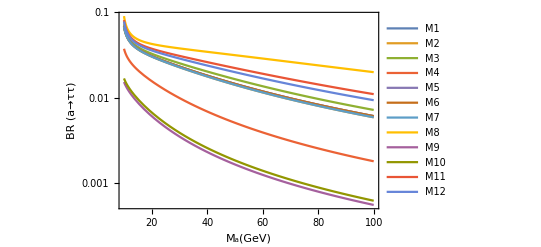

```mathematica
BRττplot = LogPlot[{BRττ/.M1,BRττ/.M2,BRττ/.M3,BRττ/.M4,BRττ/.M5,BRττ/.M6,BRττ/.M7,BRττ/.M8,BRττ/.M9,BRττ/.M10,BRττ/.M11,BRττ/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> ττ)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRtautau.eps",BRττplot]
```

BRtautau.eps

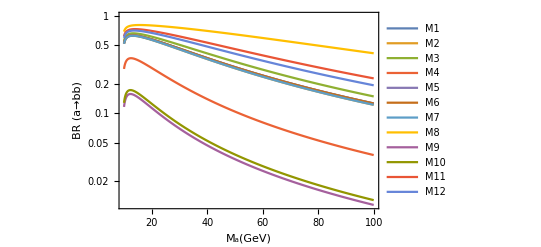

```mathematica
BRbbplot = LogPlot[{BRbb/.M1,BRbb/.M2,BRbb/.M3,BRbb/.M4,BRbb/.M5,BRbb/.M6,BRbb/.M7,BRbb/.M8,BRbb/.M9,BRbb/.M10,BRbb/.M11,BRbb/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> bb)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRbb.eps",BRbbplot]
```

BRbb.eps

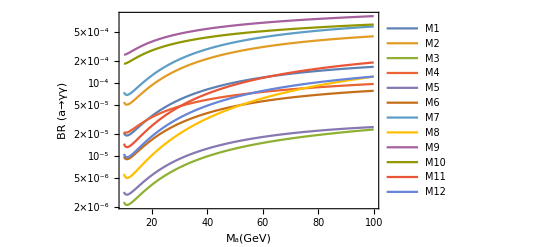

```mathematica
BRγγplot = LogPlot[{BRγγ/.M1,BRγγ/.M2,BRγγ/.M3,BRγγ/.M4,BRγγ/.M5,BRγγ/.M6,BRγγ/.M7,BRγγ/.M8,BRγγ/.M9,BRγγ/.M10,BRγγ/.M11,BRγγ/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> γγ)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRgammagamma.eps",BRγγplot]
```

BRgammagamma.eps

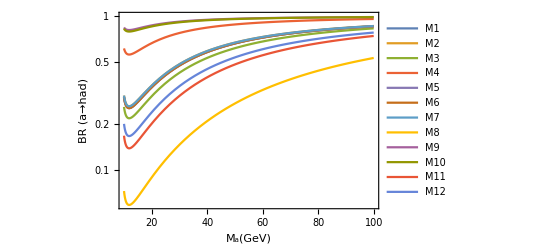

```mathematica
BRhadplot = LogPlot[{BRhad/.M1,BRhad/.M2,BRhad/.M3,BRhad/.M4,BRhad/.M5,BRhad/.M6,BRhad/.M7,BRhad/.M8,BRhad/.M9,BRhad/.M10,BRhad/.M11,BRhad/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> had)}, PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRhad.eps",BRhadplot]
```

BRhad.eps

## FeynArts

```mathematica
WriteFeynArtsOutput[LSM + LPSeudo, FlavorExpand->SU2W, FlavorExpand->SU2D]
```

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"CHpsuedo_FA","CHpseudo_FA"}];
```